```mathematica
pick[n_,d_]:=Length[Tally[RandomInteger[d-1,n]]];
```

```mathematica
probability[n0_,n1_,d_,samplesize_]:=Sum[KroneckerDelta[pick[n1,d],n0],{samplesize}]/samplesize
```

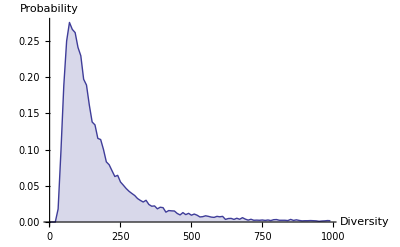

```mathematica
Interpretation[{n0=19,n1=28,up=1000},
Panel[Grid[{
{Style["Plot",Bold],SpanFromLeft},
{"Unique clones:",InputField[Dynamic[n0]]},
{"Total clones:",InputField[Dynamic[n1]]},
{"Range of plot:",InputField[Dynamic[up]]}}]],
DiscretePlot[probability[n0,n1,d,5000],{d,1,up,Round[up/100]},Joined->True, PlotRange->All,AxesLabel->{Diversity,Probability}]]
```

```mathematica
PredictedDiversity[nUnique_,nTotal_,Range_]:=(data=Table[probability[nUnique,nTotal,diversity,200],{diversity,1,Range}];
total=Sum[i, {i,data}];
corrected=data/total;
ints=Table[i,{i,1,Range}];
multiplied=corrected*ints;
Sum[i,{i,multiplied}])
```

```mathematica
Interpretation[{n0=20,n1=23,up=1000},
Panel[Grid[{
{Style["Predicted diversity",Bold],SpanFromLeft},
{"Unique clones:",InputField[Dynamic[n0]]},
{"Total clones:",InputField[Dynamic[n1]]},
{"Range of calculation:",InputField[Dynamic[up]]}}]],
 Print["Predicted diversity is:"]
N[PredictedDiversity[n0,n1,up]]]
```

Predicted diversity is:

178.938 Null